# Organic QB Polaron Master Equation.

## Inputs, all in meV.

```mathematica
(*Conversions*)
femsecond=1/(6.58 10^2) ;(* 1 femsecond  = this meV *)

(*--Cavity Parameters--*)
g= 10.6 10^-6; (*light matter coupling*)
Nm = 10^10; (*number of molecules*)
δ=0.0;(*detuning*)
kT=25.68; (* bath temperature*)
β=1/kT;

(*--Laser parameters--*)
σL=20 femsecond; (* laser width *)
η0=√Nm; (* laser amplitude *)
t0L=100 femsecond; (* laser central time *)
ηf[σL_,t0L_,t_]:=(η0/(σL*Sqrt[2*Pi])) Exp[-1/2((t-t0L)/σL)^2]; (* laser envelope function *)
(*Lindblad Decay Rates*)
κ = 1/(120 femsecond); (* Lindblad cavity leakage *)
Γd = 0.0141 ; (* Lindblad relaxation rate *)
Γu = 0.0 ; (* Lindblad drive rate *)

(*Spectral density *)
nuc=150.0;
am=0.2;
J[ω_]:=2 am ω Exp[-(ω/nuc)^2];

(*--Simulation parameters--*)
tmax=6000femsecond+t0L;
```

## Polaron Rates.

```mathematica
DD[t_?NumericQ] := Exp[NIntegrate[ (J[w]/w^2)(Coth[(β w)/2] (Cos[w t] -1) - I Sin[w t]),{w,0,∞}]]
γplus=2 g^2  Re[NIntegrate[DD[t] Exp[-0.5(Γu +Γd) t] Exp[ -I δ t],{t,0,∞},Method->"GaussKronrodRule"]];
γmin=2 g^2  Re[NIntegrate[DD[t] Exp[-0.5(Γu +Γd) t] Exp[ I δ t],{t,0,∞},Method->"GaussKronrodRule"]];
```

## Mean Field Equations.

```mathematica
(* Initial conditions *)
a0=0.0; (* <a(0)> *)
z0=({0,1}.({{1, 0}, {0, -1}}).{{0},{1}})⟦1⟧ ;(* <z(0)> *)
```

```mathematica
soln=NDSolve[{a'[t]==-(I δ + κ/2 ) a[t]  +(Nm/4) γmin  a[t]  (1 +z[t]) - (Nm/4)  γplus  a[t] (1 -z[t]) +ηf[σL,t0L,t],z'[t]==- Γd (1 + z[t]) +  γplus Conjugate[a[t]] a[t]  (1-z[t]) -γmin Conjugate[a[t]] a[t] (1 +z[t]),a[0]==a0,z[0]==z0},{a,z},{t,0,tmax}][[1]];
```

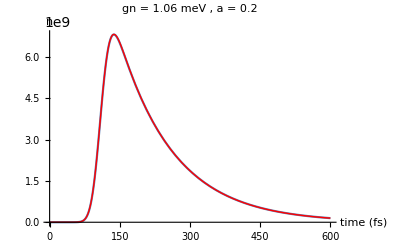

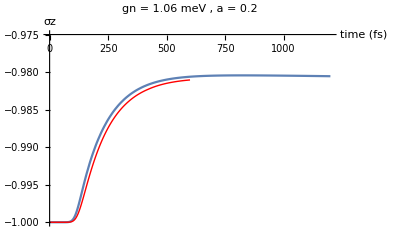

```mathematica
zsol[t_]:=Re[z[t]]/.soln
asol[t_]:=a[t]/.soln
TimeArray=BinaryReadList["/Users/ferguswilliams/Downloads/jk/examples/time.dat","Real64"];
SigzArray=BinaryReadList["/Users/ferguswilliams/Downloads/jk/examples/sig.dat", "Real64"];
AlphaArray=BinaryReadList["/Users/ferguswilliams/Downloads/jk/examples/alph.dat", "Real64"];
datalph=Transpose[{TimeArray,AlphaArray}];
datsigz=Transpose[{TimeArray,SigzArray}];
Plot[Abs[asol[t*femsecond]]^2,{t,0, 600},AxesLabel->{"time (fs)","n"},Epilog->{Red, Line[datalph]},PlotLabel->"gn = 1.06 meV , a = 0.2"]
Plot[zsol[t*femsecond],{t,0, 1200},PlotRange->{Automatic,{-1,-0.975}},AxesLabel->{"time (fs)","σz"},Epilog->{Red, Line[datsigz]},PlotLabel->"gn = 1.06 meV , a = 0.2"]
```